# Ibraheem Al-Yousef PHYS422 HW. 5 2/3/2023

## Problem 1):

```mathematica
t={62,68,73,85,90,97,101,105,112,120,125,130,138,144,149,156,163,170,175,180}//N;""
```

```mathematica
A={592,527,510,431,380,353,318,310,290,242,215,208,187,177,158,142,125,110,109,100}//N;""
```

```mathematica
data=Table[{t[[i]],Around[A[[i]],Sqrt@A[[i]]]},{i,1,Length@A}];""
```

```mathematica
data1=Table[{t[[i]],Log@A[[i]]},{i,1,Length@A}]; ""
```

### a)

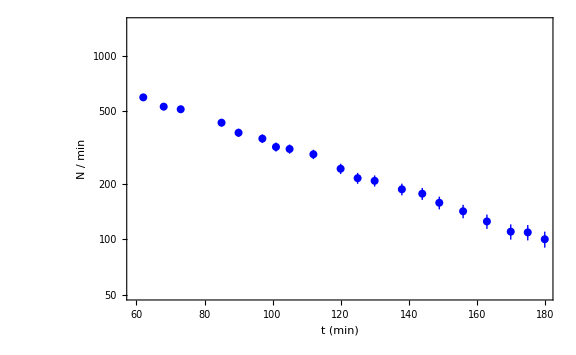

```mathematica
ListLogPlot[data,PlotTheme->{"Classic","Scientific"},PlotStyle->{PointSize[0.010],Blue},FrameTicks->All,PlotRange->{50,1500},Frame->True,FrameLabel->{"t (min)","N / min"},ImageSize->Large]
```

### b)

```mathematica
lm=LinearModelFit[data1,x,x];
```

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 7.327 | 0.0217341 | 337.12 | 1.16149×10^-35
x | -0.015213 | 0.000170749 | -89.0958 | 2.88329×10^-25

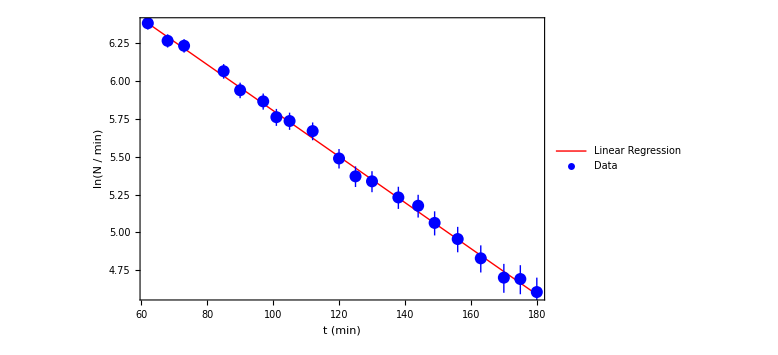

```mathematica
Show[Plot[lm[x],{x,62.,180.},PlotTheme->{"Classic","Scientific"},PlotStyle->{Thick,Red},Frame->True,FrameLabel->{"t (min)","ln(N / min)"},ImageSize->Large,PlotLegends->{"Linear Regression","Data"}],ListLogPlot[data,PlotLegends->Reverse@{"Linear Regression","Data"},PlotTheme->{"Classic","Scientific"},PlotStyle->{PointSize[0.015],Blue},Frame->True,FrameLabel->{"t (min)","N / min"},ImageSize->Large]]
```

I used Mathematica to perform the fit of 

So, the original activity will be e to the power of the intercept,  , and the slope represents -. Therefore:
 decay/min
min  s

## Problem 19):

We can assume that the ratio of^14C to^12C in the atmosphere is the same is in organic materials, and it is 1.3 x 10^-12 . Moreover,^14C has a half-life of 5700 years. So, to determine the activity, we use the following formula:
 Decay / min

## Problem 20):

From the ideal gas law, we know that . After getting the number of C atoms, we can use the same ratio to get the numbers of ^14C. The decay constant is defined as probability of decay per nucleus per unit time. So, multiplying with the number if nuclei and the time will give us the probability of decay:
 ^14C Nuclei
 %